# Risanje in reševanje enačb z Mathematico

Vaje v tem zvezku pogosto vsebujejo povezavo na dokumentacijo funkcije, ki jo morate uporabiti. Priporočamo, da dokumentacijo vsaj preletite. Včasih navodila omenijo dodatne nastavitve, tudi te poiščite v dokumentaciji.

Spodnja dva primera ilustrirata obe vrsti prirejanja.

```mathematica
(* Takojšnje prirejanje *) (* Vrednost izraza na desni se izračuna in shrani v spremenljivko na desni. Vrednost v spremenljivki ostane enaka. *)
f1=RandomInteger[{0,10}];
f1
f1
f1
```

5

5

5

```mathematica
(* Zakasnjeno prirejanje *)
(* V spremenljivko se shrani izraz na desni, njegova vrednost pa se izračuna vsakič, ko pogledamo, kakšna vrednost je v spremenljivki. *)
f2:=RandomInteger[{0,10}];
f2
f2
f2
```

3

5

4

## Funkcije in njihovi grafi

### Subsection. naloga:

1. Definirajte funkcijo f spremenljivke x s funkcijskim predpisom (x^2-1)/(x^2-4).
2. S funkcijo Plot narišite njen graf na intervalu [-5,5]. Označite še njene pole, tako da dodate nastavitev ExclusionsStyle→{{Dashed,Red}}
3. S funkcijo Solve poiščite ničle in pole funkcije f. Pri polih vam bo prišla prav še funkcija Denominator.
4. Izračunajte levo limito enega izmed polov (funkciji Limit dodate še nastavitev Direction→1).
5. Izračunajte limito funkcije, ko gre .
6. Določite stacionarne točke.
7. S funkcijo Reduce določite intervale konveksnosti (ko velja )
Za vajo lahko doma na podoben način analizirate tudi funkcijo g(x)=arctg x^2/(x^2-1).

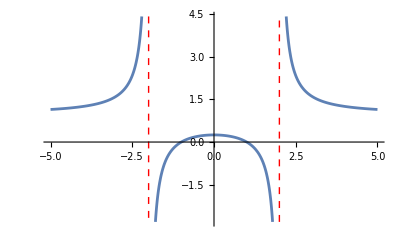

```mathematica
f[x_]:=(x^2-1)/(x^2-4)
Plot[f[x], {x, -5, 5}, ExclusionsStyle->{{Dashed,Red}}]
```

```mathematica
x/. Solve[f[x]== 0]
```

{-1,1}

```mathematica
x/. Solve[Denominator[f[x]]== 0]
```

{-2,2}

```mathematica
Limit[f[x],x->2, Direction->1]
```

-∞

```mathematica
Limit[f[x],x->Infinity]
```

1

```mathematica
x/. Solve[D[f[x],x]==0]
```

{0}

```mathematica
Reduce[f''[x]>0]
```

x<-2||x>2

```mathematica
x<-2||x>2
g[x]=arctg x^2/(x^2-1)
```

x<-2||x>2

(arctg x^2)/(-1+x^2)

### Subsection. naloga:

1. Dana je parametrično podana krivulja (((3-t) sin t)/(t+1),cos (t) sin (2t)). Definirajte jo kot funkcijo ene spremenljivke.
2. Narišite krivuljo k za  t∈[0,5] s pomočjo funkcije ParametricPlot.
3. Krivulja seče samo sebe natanko dvakrat. S pomočjo numeričnega reševanja enačb (FindRoot) poišči približek presečišč. Enačbo nastavi tako da izenačiš krivuljo, parametrizirano s parametrom t, s krivuljo, parametrizirano s parametrom s. Potem s spreminjanjem začetnih približkov parametrov t in s poskusi določiti vrednosti parametrov, pri katerih pride do samopresečič (dovolj bodo celoštevilske vrednosti, od katerih bo ena enaka 0).

```mathematica
ClearAll[p,t,s]
p[t_]:={((3-t)Sin[t])/(t+1), Cos[t]Sin[2t]}
```

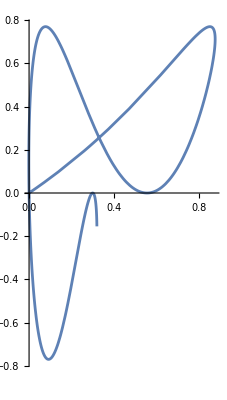

```mathematica
ParametricPlot[p[t],  {t, 0,5}]
```

```mathematica
FindRoot[p[t]==p[s],{{t,0},{s,3}} ]
```

{t→-2.79032×10^-20,s→3.14159}

### Subsection. naloga:

1. Definirajte funkcijo  g(x)=-x^3+8.
2. Narišite njen graf nad intervalom [-3,3] in ga shranite v spremenljivko graf1.
3. Izračunajte ničlo funkcije g (če želite samo realne ničle, funkciji Solve dodajte kot drugi parameter Reals).
4. Izračunajte ploščino lika, ki ga (v prvem kvadrantu) omejujeta koordinatni osi in graf te funkcije.
5. V spremenljivko  graf2 shranite graf funkcije nad intervalom, po katerem ste integrirali. Grafu dodajte določilo Filling→Axis.
6. Postavite oba grafa na isti koordinatni sistem s funkcijo Show.

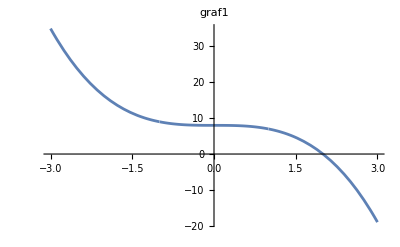

```mathematica
g[x_]:=-x^(3) +8
graf1=Plot[g[x],{x, -3, 3},PlotLabel->"graf1"]
```

```mathematica
x/. Solve[g[x]==0, Reals]
```

{x,0}

```mathematica
Integrate[g[x], {x,0, 2}]
```

Integrate::idiv: Integral of (arctg x^2)/(-1+x^2) does not converge on {0,2}.

∫_0^2 (arctg x^2)/(-1+x^2)ⅆx

```mathematica
12
```

12

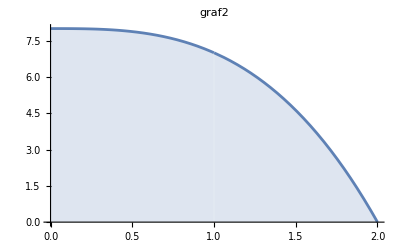

```mathematica
graf2=Plot[g[x],{x,0,2}, Filling->Axis, PlotLabel->"graf2"]
```

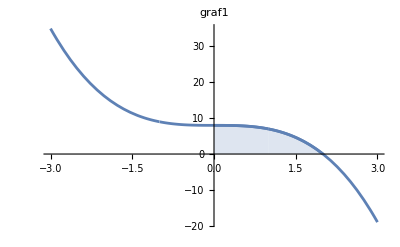

```mathematica
Show[graf1,graf2]
```

### Subsection. naloga:

1. Definiraj funkciji  s(x)=x^2-8  in  z(x)=-x^2+10  ter nariši njuna grafa. Funkcija Plot bo narisala več grafov, če jih podate naštete v seznamu (v zavitih oklepajih, ločene z vejicami).
2. Poiščite njuni presečišči.
3. Izračunajte ploščino lika, ki ga omejujeta grafa teh dveh funkcij.
4. Še enkrat narišite grafa obeh funkcij, le da bo tokrat območje, katerega ploščino ste izračunali, pobarvano. Filling nastavite na {1→{2}} (kaj to naredi, poiščite v dokumentaciji nastavitve pod Applications).

```mathematica
s[x_]:=x^2 -8
```

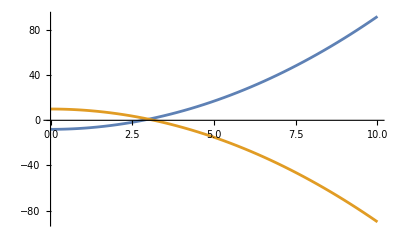

```mathematica
z[x_]:=-x^2 +10
Plot[{s[x],z[x]}, {x,0,10}]
```

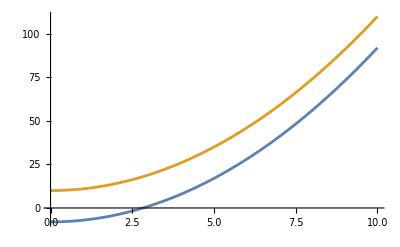

-Graphics-

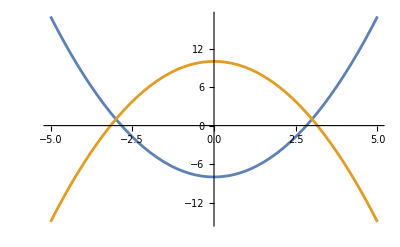

```mathematica
graf1=Plot[{s[x],z[x]},{x, -5, 5}]
```

```mathematica
presec=x/. Solve[s[x]==z[x]]
```

{-3,3}

```mathematica
Integrate[z[x]-s[x], {x, presec[[1]], presec[[2]]}]
```

72

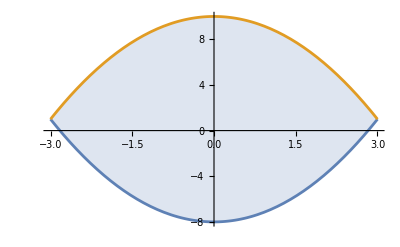

```mathematica
graf2=Plot[{s[x],z[x]}, {x, -3, 3}, Filling->{1->{2}}]
```

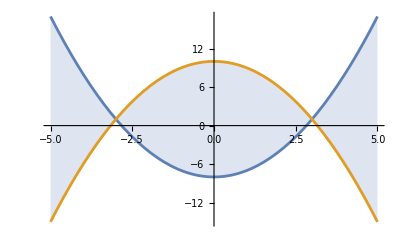

```mathematica
graf3=Plot[{s[x],z[x]}, {x, -5, 5}, Filling->{1->{2}}]
```

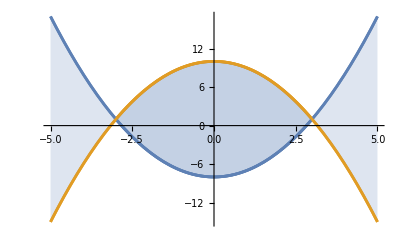

```mathematica
Show[graf1, graf2, graf3]
```

## Reševanje enačb

### Subsection. naloga:

1. Numerično izračunaj ničle polinoma  x^7-2 x^6-x^5-2 x^4+12 x^2-x+1. 
2. Preberite dokumentacijo funkcije NSolve in izračunajte samo realne ničle.

```mathematica
Clearall{f, x}
```

{Clearall f,Clearall x}

```mathematica
(* x^7-2x^6-x^5 - 2x^4 + 12x^2 - x + 1 *)
NSolve[x^7-2x^6-x^5 - 2x^4 + 12x^2 - x + 1==0, x]
```

{{x→-1.37527},{x→-0.356206-1.47367 ⅈ},{x→-0.356206+1.47367 ⅈ},{x→0.040941-0.283889 ⅈ},{x→0.040941+0.283889 ⅈ},{x→1.59494},{x→2.41086}}

```mathematica
NSolve[x^7-2x^6-x^5 - 2x^4 + 12x^2 - x + 1, x, Reals]
```

{{x→-1.37527},{x→1.59494},{x→2.41086}}

```mathematica
f[x_]:=x^7-2x^6-x^5 - 2x^4 + 12x^2 - x + 1
```

```mathematica
NSolve[f[x]==0, x]
```

{{x→-1.37527},{x→-0.356206-1.47367 ⅈ},{x→-0.356206+1.47367 ⅈ},{x→0.040941-0.283889 ⅈ},{x→0.040941+0.283889 ⅈ},{x→1.59494},{x→2.41086}}

### Subsection. naloga:

Določi vsa realna števila, ki zadoščajo neenačbi  (|x-3|)/(x+1)>√(3-2x)

```mathematica
Reduce[Abs[x-3]/(x+1)>√(3-2x)]
```

-1<x<1||1<x≤3/2

### Subsection. naloga:

S funkcijo Solve rešujemo enačbe. Najbolj enostavno jo uporabimo, kadar imamo opravka z eno samo spremenljivko:
- Poiščite vsa kompleksna števila, ki zadoščajo enačbi  z̄=z^2. Za konjugiranje lahko uporabite *, funkcijo Conjugate ali pa znak Esc co Esc.
- Določite vrednost parametra a v enačbi (2a x+3a)/(3a + 5x)=(3a-4)/(3a - 5x), da bo  x=2  rešitev enačbe.

```mathematica
Solve[Conjugate[z]==z^2]
```

{{z→0},{z→1},{z→-1/2-(ⅈ √3)/2},{z→-1/2+(ⅈ √3)/2}}

```mathematica
Clearall[a, x ]
```

Clearall[a,x]

Set::write: Tag Times in (3 a+2 ax)/(3 a+5 x) is Protected.

```mathematica
enacba=(2a x+3a)/(3a+5x)==(3a-4)/(3a-5x)
```

(3 a+2 a x)/(3 a+5 x)==(-4+3 a)/(3 a-5 x)

```mathematica
(3 a+2 a x)/(3 a+5 x)==(-4+3 a)/(3 a-5 x)
```

(3 a+2 a x)/(3 a+5 x)==(-4+3 a)/(3 a-5 x)

```mathematica
enacba/. {x->2}
```

(7 a)/(10+3 a)==(-4+3 a)/(-10+3 a)

```mathematica
Solve [enacba /. {x -> 2}]
```

{{a→1/3 (11-√91)},{a→1/3 (11+√91)}}

```mathematica
(3 a+2 a x)/(10+3 a)==(-4+3 a)/(-10+3 a)
r=Solve[enacba/. {x->2}, a]
enacba/. r/. {x->2}
```

(3 a+2 a x)/(10+3 a)==(-4+3 a)/(-10+3 a)

{{a→1/3 (11-√91)},{a→1/3 (11+√91)}}

{True,True}

### Subsection. naloga:

Rešujemo lahko tudi več enačb z več neznankami. V tem primeru enačbe naštejemo v zavite oklepaje (ločene naj bodo z vejicami).
Določite k in n tako, da bo šla premica y=k x+n skozi točki (-2,3) in (6,-1).

```mathematica
Clearall[x]
kn= Solve[{3== -2k+n, -1== 6k+n}]
```

Clearall[x]

{{k→-1/2,n→2}}

```mathematica
premica = y == k x + n
```

y==n+k x

```mathematica
premica /. Solve[{3== -2k+n, -1== 6k+n}]
```

{y==2-x/2}

```mathematica
T1={x->-2, y->3};
T2= {x->6, y->-1};
```

```mathematica
Solve[y==k x+n/.{T1,T2}, {k, n}]
```

{{k→-1/2,n→2}}

```mathematica
{{k->-1/2,n->2}}
kn= Solve[y==k x+n/.{T1,T2}, {k, n}]
```

{{k→-1/2,n→2}}

{{k→-1/2,n→2}}

```mathematica
Clearall[x]
```

Clearall[x]

```mathematica
y==k x+n/.kn
```

{y==2-x/2}

### Subsection. naloga:

Sin je 3 leta starejši od hčere, mati pa je 23 let starejša od sina. Pred 6 leti je imela mati 4 krat toliko let kot sin in hči skupaj. Koliko je star vsak od njih? Napišite enačbe in jih rešite s pomočjo funkcije Solve.

```mathematica
ClearAll[s]
```

```mathematica
Solve[{s==h+3,m== h+3+23, 4 (h-6+h-3)==m-6}, {m,h,s}]
```

{{m→34,h→8,s→11}}

### Subsection. naloga:

Koliko začetnih členov zaporedja s splošnim členom  a_n=16-2n  moramo sešteti, da bo vsota enaka 36? Začnite s tem, da napišete vsoto ∑_(i=1)^k a_i, nato pa ustrezno enačbo.

```mathematica
f[k_]:=∑_(i=1)^k (16-2i)
k1=Solve[f[k]==36]
```

{{k→3},{k→12}}

```mathematica
{{k->3},{k->12}}
f[k]/.k1
```

{{k→3},{k→12}}

{36,36}